## Hw9

Shahaf Zohar 205978000
Roey Salah 206115438

#### Function

```mathematica
(*Power Law functions*)
DegreeFreq[g_]:=Map[{#⟦1⟧,#⟦2⟧/VertexCount[g]}&,Tally[VertexDegree[g]]];
CumDigDist[g_,min_,max_]:=Module[{df,cm,minpos,maxpos},df=Sort[DegreeFreq[g],#1⟦1⟧<#2⟦1⟧&];
minpos=First@First@Position[df⟦All,1⟧,min];
maxpos=First@First@Position[df⟦All,1⟧,max];
cm=Reverse[Accumulate[Reverse[df⟦All,2⟧]]];
Transpose[{df⟦minpos;;maxpos,1⟧,cm⟦minpos;;maxpos⟧}]]
(*Shift diagram functions*)
RenameGraphN[g_, sl_]:=Module[{G= g,VrDg = sl,VrLs,VrLst,SVrLst,NewName,edges,NewEdges, ed},
VrLs =VertexList[G];
VrLst = Table[{VrDg[[i]], VrLs[[i]]},{i,Length[VrDg]}];
SVrLst= Sort[VrLst,#1[[1]]>#2[[1]]&];
NewName = Table[SVrLst[[i]][[2]],{i,Length[VrDg]}];
edges = EdgeList[G];
If[DirectedGraphQ[G], 
NewEdges =Table[Position[NewName,edges[[i]][[1]]][[1]][[1]]->Position[NewName,edges[[i]][[2]]][[1]][[1]],{i,Length[edges]}],
NewEdges =Table[Position[NewName,edges[[i]][[1]]][[1]][[1]]<->Position[NewName,edges[[i]][[2]]][[1]][[1]],{i,Length[edges]}]];
Graph[Range[Length[VrLst]],NewEdges]]
SymmetryPoint[G_]:=Module[{s,EE={},EP={},PE={},PP={},ee=0,ep=0,pe=0,pp=0,tc,bc,tr,br},s=Length[VertexList[G]];
ee=AdjacencyMatrix[G]⟦1⟧⟦1⟧;
pe=Total[Total[Take[AdjacencyMatrix[G],{2,s},{1,1}]]];
ep=Total[Total[Take[AdjacencyMatrix[G],{1,1},{2,s}]]];
pp=Total[Total[Take[AdjacencyMatrix[G],{2,s},{2,s}]]];
EE={0,ee/2};
EP={0,ep/2};
PE={0,pe/2};
PP={EdgeCount[G],pp/2};
For[i=1,i<s-1,i++;
tc=Total[Total[Take[AdjacencyMatrix[G],{1,i-1},{i,i}]]];
bc=Total[Total[Take[AdjacencyMatrix[G],{i+1,s},{i,i}]]];
tr=Total[Total[Take[AdjacencyMatrix[G],{i,i},{1,i-1}]]];
br=Total[Total[Take[AdjacencyMatrix[G],{i,i},{i+1,s}]]];
ee=ee+tc+tr+AdjacencyMatrix[G]⟦i⟧⟦i⟧;
ep=ep+br-tc;
pe=pe+bc-tr;
pp=pp-bc-br-AdjacencyMatrix[G]⟦i⟧⟦i⟧;;EE=Join[EE,{ee/2}];
EP=Join[EP,{ep/2}];
PE=Join[PE,{pe/2}];
PP=Join[PP,{pp/2}];];
{EE,EP+PE,PP}]
PlotShift[graph_,title_String]:=Module[{a},
a=ListLinePlot[SymmetryPoint[RenameGraphN[graph,VertexDegree[graph]]],PlotLegends->Placed[{"I(ℰ,ℰ)","I(𝒫,ℰ)","I(𝒫,𝒫)"},Bottom],PlotRange->All,AxesLabel->{"Core Size","Number of Edges"},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},PlotLabel->Row[{"Shift diagram - ",title," model"}]];
Return[a];
]
(*Community detection function, using the Louvaion method from HW7*)
(*Need to install this packet:*)
SetDirectory[NotebookDirectory[]];
PacletUninstall["IGraphM"];
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"];
<<"IGraphM`";
IGVersion[];
CommunityDetectionIGM[graph_,title_String]:=Module[{cl,clcl,len,tot,plot},
cl=IGCommunitiesMultilevel[graph];
clcl=cl["Communities"];
len=Length[clcl];
tot=Table[Length[clcl[[i]]],{i,1,Length[clcl]}];
plot=BarChart[tot,ChartLabels->Range[Length[clcl]],ChartStyle->"Pastel",LabelingFunction->(Placed[#,Center]&),PlotLabel->Row[{"Community detection - ",title," model"}]];
Return[plot];
]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

1. Find a network with power law degree distribution . Plot the degree distribution and try to find power exponent β .

```mathematica
net=ExampleData[{"NetworkGraph","DiseaseGeneNetwork"}];
Print["Vertex Count for the network: ",VertexCount[net]]
maxD=Max[VertexDegree[net]];
meanD=Mean[VertexDegree[net]]//N;
Print["The mean of Vertex Count for the network: ",meanD]
Print["The max  Degree of the network: ",maxD]
```

Vertex Count for the network: 1777

The mean of Vertex Count for the network: 8.43106

The max  Degree of the network: 70

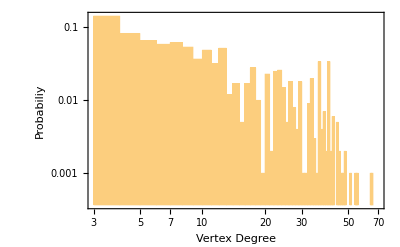

4.20769-2.2119 x

The power exponent β is: 2.2119→ 2≤β≤3

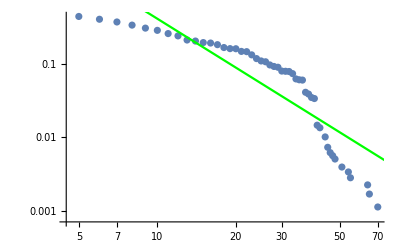

```mathematica
Histogram[VertexDegree[net],{3,maxD,1},"Probability",ScalingFunctions->{"Log","Log"},FrameLabel->{"Vertex Degree","Probabiliy"},Frame->True]
Powerfit=Fit[Log[CumDigDist[net,5,maxD]],{1,x},x]
beta=-Powerfit[[2]][[1]];
Print[Style["The power exponent β is: ",20], beta,"→ 2≤β≤3"]
Show[ListLogLogPlot[CumDigDist[net,5,maxD]],Plot[Powerfit,{x,1,58},PlotStyle->Green]]
```

2. Generate the symmetry point graph for PA with sevral sizes (on what fraction it is happends? what is the "core" fraction)

Vertex Count for the PA: 1777

The mean of Vertex Count for the PA: 7.98875

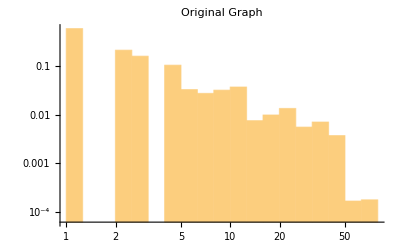
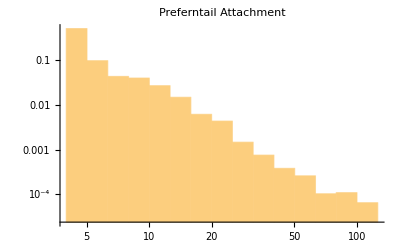

2.80841-1.93525 x

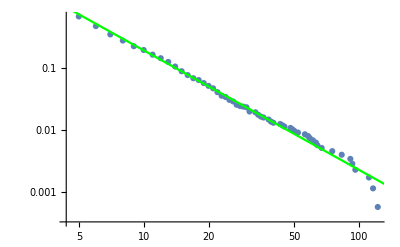

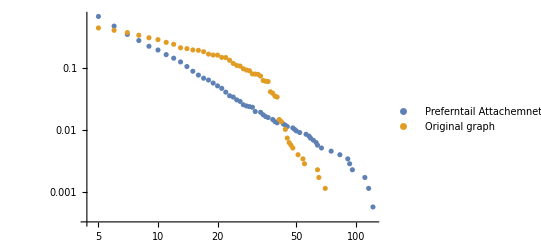

```mathematica
Pa=RandomGraph[BarabasiAlbertGraphDistribution[VertexCount[net],Round[EdgeCount[net]/VertexCount[net]]]];
Print["Vertex Count for the PA: ",VertexCount[Pa]]
Print["The mean of Vertex Count for the PA: ",Mean[VertexDegree[Pa]]//N]
{Histogram[VertexDegree[net],{"Log",15},{"Log","PDF"},PlotLabel->"Original Graph"],Histogram[VertexDegree[Pa],{"Log",15},{"Log","PDF"},PlotLabel->"Preferntail Attachment"]}
PowerfitPa=Fit[Log[CumDigDist[Pa,5,Max[VertexDegree[Pa]]]],{1,x},x]
Show[ListLogLogPlot[CumDigDist[Pa,5,Max[VertexDegree[Pa]]]],Plot[PowerfitPa,{x,1,58},PlotStyle->Green]]
ListLogLogPlot[{CumDigDist[Pa,5,Max[VertexDegree[Pa]]],CumDigDist[net,5,Max[VertexDegree[net]]]},PlotLegends->{"Preferntail Attachemnet","Original graph"}]
(*not work*)
(*spPA=PlotShift[Pa,"PA"]*)
```

3. Add Preferential Attachment to the models you check "Network of Throne" with . Like we did in home work 8

```mathematica
(*Load the netork*)
SetDirectory[NotebookDirectory[]];
file=Rest[Import["stormofswords.csv"]];
tribes=Import["tribes.csv"];
nodes=Flatten[tribes⟦All,1⟧];
nodesTribe=Flatten[tribes⟦All,2⟧];
edges=#⟦1⟧<->#⟦2⟧&/@file⟦All,{1,2}⟧;
G=Graph[nodes,edges];
```

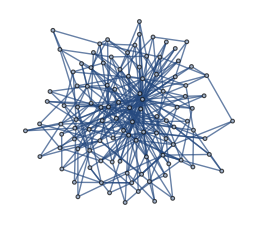

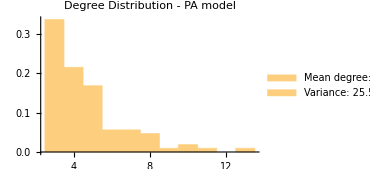

```mathematica
(*Creat the PA - Graph*)
PaG=RandomGraph[BarabasiAlbertGraphDistribution[VertexCount[G],Round[EdgeCount[G]/VertexCount[G]]]]
(*Degree distribution*)
degDisPa=Histogram[VertexDegree[PaG],{1},"Probability",PlotLabel->"Degree Distribution - PA model",ChartLegends->Placed[{StringForm["Mean degree: ``",Mean[VertexDegree[PaG]]//N],StringForm["Variance: ``",Variance[VertexDegree[PaG]]//N]},Bottom]]
```

```mathematica
(*Giant component*)
GiantComponentG=Length[First[ConnectedComponents[PaG]]];
Print["Giant component: ",GiantComponentG]
(*Average distance, to avoide ∞ in un-connected graph, I took the largest connected components for that*)
AverageDistancePa=Mean[Flatten[GraphDistanceMatrix[Subgraph[PaG,First[ConnectedComponents[PaG]]]]]]//N;
Print["Average distance: ",AverageDistancePa]
```

Giant component: 107

Average distance: 2.5866

```mathematica
(*Shift diagram, not work at all*)
(*sdPa=PlotShift[PaG,"PA"]*)
```

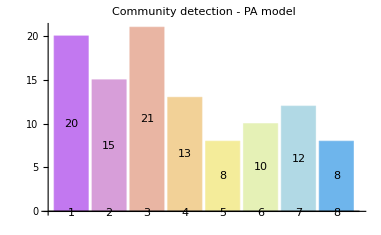

```mathematica
(*Community detection, for Throne model I plot the true communities by tribes*)
CommunityDetectionPa=CommunityDetectionIGM[PaG,"PA"]
```

## Discuss our finding

### For the graph DiseaseGeneNetwork network

for the discuss models, G (n, p) and G (n, m) models generate random graphs with varying edge configurations, while the block model and configuration model aim to simplify and analyze specific aspects of the original graph, such as community structure or degree distribution, respectively . The choice of model depends on the specific characteristics of the original graph that we want to preserve or explore . 
The average distance and giant component are similarly present, and we can see that expected value (Degree) approximately the same for each model and the result is 
N*P = 1777*0.0622465~110.612

```mathematica
NP = 1777*0.0622465
```

110.612

and for the Diameter for all model is the same again and the calculate D~log (1777) = 3.249 ,log (110.612) = 2.043 . We can see that is less then log (107) = 4.672 as we expected . In summary, the differences between the original network and the graph models arise due to the specific generation methods employed by each model . These differences are purposeful and serve
different analytical or modeling objectives, such as studying random graphs, understanding community structures, or analyzing degree distributions . The choice of model depends on the research.  The average distance  is around  log (n)/log(z)= (log (1777)/log(110.612) ~ 1.59).

```mathematica
Log2[1777]/Log2[110.612]
```

1.59002

### For the graph Throne network

N*P = 107*0.0622465~6.6
different analytical or modeling objectives, such as studying random graphs, understanding community structures, or analyzing degree distributions . The choice of model depends on the research .  The average distance  is around  log (n)/log (z) = log (107)/log (6.6) ~ 2.47624

```mathematica
Log2[107]/Log2[6.6]
```

2.47624